Final ODE for the perturbation mode f(x):

-ωp^2 f[x]-f''[x]==0

General solution for f(x):

{{f[x]→C[1] Cos[x ωp]+C[2] Sin[x ωp]}}

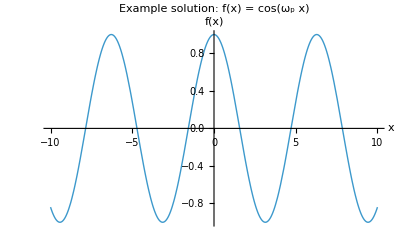

-Graphics3D-

Einstein tensor G_{μν} evaluated at (t=1, x=1, y=0, z=0):

(0.000270293 | 0. | 0. | 0.
0. | 0.00482331 | 0. | 0.
0. | 0. | 0.00482331 | 0.
0. | 0. | 0. | 0.00482331)

Visualizing g_tt(t,x):

-Graphics3D-

Flare-out condition (d/dr e^{-2Φ}) at r = R0, t = 0:

d/dr[e^{-2Φ}] = 2.

Flare-out condition satisfied at throat.

Stress-Energy Tensor T_{μν} at (t=1, x=1, y=0, z=0):

(0.0000107546 | 0. | 0. | 0.
0. | 0.000191913 | 0. | 0.
0. | 0. | 0.000191913 | 0.
0. | 0. | 0. | 0.000191913)

Energy density ρ = T_{00} = 0.0000107546

Radial pressure p_r = T_{11} = 0.000191913

Angular pressure p_θ = T_{22} = 0.000191913

Angular pressure p_φ = T_{33} = 0.000191913

Null Energy Condition along radial null vector (1,1,0,0):

T_{μν} k^μ k^ν = 0.000202668

NEC satisfied at this point.

0.9 | 0.000202668 | Satisfied
1. | 0.000202668 | Satisfied
1.1 | 0.000202668 | Satisfied
1.2 | 0.000202668 | Satisfied
1.3 | 0.000202668 | Satisfied
1.4 | 0.000202668 | Satisfied
1.5 | 0.000202668 | Satisfied
1.6 | 0.000202668 | Satisfied
1.7 | 0.000202668 | Satisfied
1.8 | 0.000202668 | Satisfied
1.9 | 0.000202668 | Satisfied
2. | 0.000202668 | Satisfied

0.5 | 2. | Flare-out OK
0.6 | 2. | Flare-out OK
0.7 | 2. | Flare-out OK
0.8 | 2. | Flare-out OK
0.9 | 2. | Flare-out OK
1. | 2. | Flare-out OK
1.1 | 2. | Flare-out OK
1.2 | 2. | Flare-out OK
1.3 | 2. | Flare-out OK
1.4 | 2. | Flare-out OK
1.5 | 2. | Flare-out OK
1.6 | 2. | Flare-out OK
1.7 | 2. | Flare-out OK
1.8 | 2. | Flare-out OK
1.9 | 2. | Flare-out OK
2. | 2. | Flare-out OK
2.1 | 2. | Flare-out OK
2.2 | 2. | Flare-out OK
2.3 | 2. | Flare-out OK
2.4 | 2. | Flare-out OK
2.5 | 2. | Flare-out OK
2.6 | 2. | Flare-out OK
2.7 | 2. | Flare-out OK
2.8 | 2. | Flare-out OK
2.9 | 2. | Flare-out OK
3. | 2. | Flare-out OK

```mathematica
(*Clear all previous definitions*)ClearAll["Global`*"];

(*Set basic parameters*)
R0=1;              (*Wormhole throat radius*)
A=1;               (*Static potential amplitude*)
w=0.5;             (*Width of transition region*)
ϵ=0.01;   (*Small regularization parameter*)
ϵp=0.05;  (*Perturbation amplitude*)
ω=0.2;      (*Background oscillation frequency*)
ωp=Symbol["ωp"];  (*Frequency of the perturbation mode*)

(* ===Time-dependent wormhole potential with smooth throat===*)
Rthroat[t_]:=R0*(1+0.1*Exp[-t/10]*Cos[ω t]);
p=10; (*smoothness degree:higher=closer to Max*)
(*=== Negative Potential to allow flare-out*)
Φ[t_,x_,y_,z_]:=Module[{r},r=Max[Sqrt[x^2+y^2+z^2],Rthroat[t]];
-A*(1-R0/r)*Exp[-((r-R0)^2)/w^2]];

(*Φ[t_,x_,y_,z_]:=Module[{r},r=Max[Sqrt[x^2+y^2+z^2],Rthroat[t]];
A*(1-R0/r)*Exp[-((r-R0)^2)/w^2]];*)


(* ===Linear perturbation over the wormhole background===*)
(*Assume δΦ(t,x)=f(x)*Exp[I ωₚ t]*)

(*Define symbolic function and coordinates*)
Clear[fSym,x,t];
fSym=f[x];  (*Spatial mode*)
deltaPhiAnsatz=fSym*Exp[I*ωp*t];

(*Compute second derivatives*)
secondTimeDerivative=D[deltaPhiAnsatz,{t,2}]//Simplify;
secondSpaceDerivative=D[deltaPhiAnsatz,{x,2}]//Simplify;

(*Construct linear wave equation:□ δΦ=0*)
waveEquationFull=secondTimeDerivative-secondSpaceDerivative==0;

(*Divide out the exponential factor to isolate the spatial equation*)
(*Note:this step is purely algebraic and done before DSolve*)
waveEquationReduced=waveEquationFull/. Exp[I*ωp*t]->1;

(*Print final ODE*)
Print["\nFinal ODE for the perturbation mode f(x):"];
Print[waveEquationReduced];

(* ===Solve the ODE analytically===*)
solution=DSolve[waveEquationReduced,f[x],x];

(*Output solution*)
Print["\nGeneral solution for f(x):"];
Print[solution];

(*Optional:Visualize a specific solution*)
(*Example:ωₚ=1,C[1]=1,C[2]=0*)
exampleSolution=f[x]/. solution[[1]]/. {ωp->1,C[2]->0,C[1]->1};

Plot[exampleSolution,{x,-10,10},PlotLabel->"Example solution: f(x) = cos(ωₚ x)",AxesLabel->{"x","f(x)"},PlotStyle->Thick]

(* ===Animated 2D standing wave:δΦ(t,x)===*)(*Set numerical values*)ωpVal=1;   (*Mode frequency*)
ϵpVal=0.05;

(*Define real-valued standing wave*)
deltaPhiReal[t_,x_]:=ϵpVal*Cos[ωpVal*x]*Cos[ωpVal*t];

(*Animate the perturbation over time*)
Manipulate[Plot[deltaPhiReal[t,x],{x,-10,10},PlotRange->{-0.1,0.1},PlotLabel->Row[{"δΦ(t,x) at t = ",NumberForm[t,{3,1}]}],AxesLabel->{"x","δΦ"},PlotStyle->Thick],{t,0,2*Pi/ωpVal,0.05}]

(*Parameters*)ϵp=0.05;
ωp=1;

(*Real-valued solution for δΦ(t,r)*)
deltaPhi3D[t_,r_]:=ϵp*Cos[ωp*r]*Cos[ωp*t];

(*3D surface plot over time and radius*)
Plot3D[deltaPhi3D[t,r],{r,-10,10},{t,0,2*Pi/ωp},PlotRange->All,AxesLabel->{"r","t","δΦ(t, r)"},PlotLabel->"Radial Wormhole Perturbation Field δΦ(t, r)",MeshFunctions->{#3&},MeshStyle->Directive[Red,Dashed],ColorFunction->"ThermometerColors",PlotPoints->100,Lighting->"Neutral"]
(* ===Metric definition===*)gtt[t_,x_,y_,z_]:=-Exp[2*Φ[t,x,y,z]];
gxx[t_,x_,y_,z_]:=Exp[-2*Φ[t,x,y,z]];
gyy[t_,x_,y_,z_]:=Exp[-2*Φ[t,x,y,z]];
gzz[t_,x_,y_,z_]:=Exp[-2*Φ[t,x,y,z]];

(*Build the full metric tensor*)
metric={{gtt[t,x,y,z],0,0,0},{0,gxx[t,x,y,z],0,0},{0,0,gyy[t,x,y,z],0},{0,0,0,gzz[t,x,y,z]}};

coords={t,x,y,z};
invMetric=TimeConstrained[Simplify[Inverse[metric]],5,Inverse[metric]];

(*Compute Christoffel symbols Γ^μ_{νρ}*)
Γ[μ_,ν_,ρ_]:=Sum[1/2*invMetric[[μ,σ]]*(D[metric[[σ,ν]],coords[[ρ]]]+D[metric[[σ,ρ]],coords[[ν]]]-D[metric[[ν,ρ]],coords[[σ]]]),{σ,1,4}];

(*Compute Ricci tensor R_{μν}*)
Riemann[μ_,ν_,ρ_,σ_]:=D[Γ[μ,ν,σ],coords[[ρ]]]-D[Γ[μ,ν,ρ],coords[[σ]]]+Sum[Γ[μ,κ,ρ]*Γ[κ,ν,σ]-Γ[μ,κ,σ]*Γ[κ,ν,ρ],{κ,1,4}];

Ricci[μ_,ν_]:=Sum[Riemann[σ,μ,σ,ν],{σ,1,4}];

RicciScalar:=Sum[invMetric[[μ,ν]]*Ricci[μ,ν],{μ,1,4},{ν,1,4}];

(*Compute Einstein tensor G_{μν}*)
Einstein[μ_,ν_]:=TimeConstrained[Simplify[Ricci[μ,ν]-1/2*metric[[μ,ν]]*RicciScalar],5,Ricci[μ,ν]-1/2*metric[[μ,ν]]*RicciScalar];

(* ===Numerical evaluation of Einstein tensor at a point===*)
params={x->1,y->0,z->0,t->1,A->1,R0->1,w->0.5,ω->0.2};

Print["\nEinstein tensor G_{μν} evaluated at (t=1, x=1, y=0, z=0):"];
einsteinAtPoint=Table[Einstein[μ,ν]/. params//Simplify,{μ,1,4},{ν,1,4}];
MatrixForm[einsteinAtPoint]

(* ===Plot g_tt(t,x) to detect horizons===*)
Print["\nVisualizing g_tt(t,x):"];

Plot3D[gtt[t,x,0,0]/. {A->1,R0->1,w->0.5,ω->0.2},{x,-5,5},{t,0,10},PlotRange->All,AxesLabel->{"x","t","g_tt"},PlotLabel->"Time evolution of g_tt(t,x)"]

(* ===Flare-out condition:d/dr (e^{-2Φ(r,t)}) at r=R0===*)Clear[r,t];

(*Corrected Φ(r,t) with negative sign*)
PhiRT[r_,t_]:=-A*(1-R0/r)*Exp[-((r-R0)^2)/w^2]/. {A->1,R0->1,w->0.5};

(*Compute derivative before substituting r=R0*)
flareOutExpr=Exp[-2*PhiRT[r,t]];
flareOutDerivative=D[flareOutExpr,r];

Print["\nFlare-out condition (d/dr e^{-2Φ}) at r = R0, t = 0:"];
flareOutAtThroat=flareOutDerivative/. {r->1,t->0}//N;
Print["d/dr[e^{-2Φ}] = ",flareOutAtThroat];

If[flareOutAtThroat>0,Print["Flare-out condition satisfied at throat."],Print["Flare-out condition violated at throat."]];

(* ===Compute Stress-Energy Tensor:T_{μν}=(1/8π) G_{μν}===*)stressEnergyAtPoint=(1/(8*Pi))*einsteinAtPoint;

Print["\nStress-Energy Tensor T_{μν} at (t=1, x=1, y=0, z=0):"];
MatrixForm[stressEnergyAtPoint]

(* ===Interpret Components===*)
rho=stressEnergyAtPoint[[1,1]];        (*Energy density*)
pr=stressEnergyAtPoint[[2,2]];         (*Radial pressure*)
ptheta=stressEnergyAtPoint[[3,3]];     (*Angular θ pressure*)
pphi=stressEnergyAtPoint[[4,4]];       (*Angular φ pressure*)

Print["\nEnergy density ρ = T_{00} = ",rho//N];
Print["Radial pressure p_r = T_{11} = ",pr//N];
Print["Angular pressure p_θ = T_{22} = ",ptheta//N];
Print["Angular pressure p_φ = T_{33} = ",pphi//N];

(* ===Check Null Energy Condition (NEC):T_{μν} k^μ k^ν>=0===*)
(*Choose radial null vector:k^μ=(1,1,0,0)*)
kμ={1,1,0,0};

(*Compute T_{μν} k^μ k^ν=sum over μ,ν*)
nec=Sum[stressEnergyAtPoint[[μ,ν]]*kμ[[μ]]*kμ[[ν]],{μ,1,4},{ν,1,4}];

Print["\nNull Energy Condition along radial null vector (1,1,0,0):"];
Print["T_{μν} k^μ k^ν = ",nec//N];
If[nec>=0,Print["NEC satisfied at this point."],Print["NEC violated at this point."]];

Table[With[{xval=r},kμ={1,1,0,0};
Tμν=stressEnergyAtPoint/. {x->xval,t->0};
necVal=Sum[Tμν[[μ,ν]]*kμ[[μ]]*kμ[[ν]],{μ,1,4},{ν,1,4}];
{xval,necVal,If[necVal>=0,"Satisfied","Violated"]}],{r,0.9,2,0.1}]//TableForm

Table[Module[{phi,ddr},phi[r_]:=-(1-1/r)*Exp[-((r-1)^2)/wval^2];(*Fixed sign*)ddr=D[Exp[-2*phi[r]],r]/. r->1//N;
{wval,ddr,If[ddr>0,"Flare-out OK","Violated"]}],{wval,0.5,3,0.1}]//TableForm
```